```mathematica
Needs["NVSim`"]
```

Using QuantumUtils version 213.

## Introduction

Make sure you have installed NVSim: just open up the Install.nb file, and click the 
menu item Evaluation->Evaluate Menu.

You are encouraged to look at the code in NVSim.m, lots of effort has been put into making it readable.

## Making NV Hamiltonians

The function used for making NV Hamiltonias is NVHamiltionian. You can run it empty and it will output just the ZFS Hamiltonian:

```mathematica
NVHamiltonian[]//MatrixForm
```

(1.80956×10^10 | 0. | 0.
0. | 0. | 0.
0. | 0. | 1.80956×10^10)

You can add terms to the Hamiltonian by calling it with a parameter object. By parameter object I just mean a list of Rules, for example:

```mathematica
params={"B"->{10,0,0},"nitrogenIsotope"->15};
```

This parameter object has set the field to 10 Gauss in the z-direction (B is in spherical coordinates), and added the nitrogen in with spin-1/2. The possible parameters are listed in the next section.
Now if we call NVHamiltonian with params, we will get what we expect:

```mathematica
NVHamiltonian[params]//MatrixForm
```

(1.82861×10^10 | 0. | 0. | 0. | 0. | 0.
0. | 1.82572×10^10 | 1.86601×10^7 | 0. | 0. | 0.
0. | 1.86601×10^7 | -4316. | 0. | 0. | 0.
0. | 0. | 0. | 4316. | 1.86601×10^7 | 0.
0. | 0. | 0. | 1.86601×10^7 | 1.7905×10^10 | 0.
0. | 0. | 0. | 0. | 0. | 1.79339×10^10)

The Hilbert space factors will always be ordered as follows:
ℋ_NV⊗ℋ_Nitrogen⊗ℋ_(Carbon 1)⊗ℋ_(Carbon 2)⊗...⊗ℋ_(Carbon m)
The order of the carbons is decided by the “carbonPositions” parameter (see below). If you set “nitrogenIsotope” to 0, or if you omit it from the paramater list, it will be left out completely, as we saw when we called NVHamiltonian[] with no parameters.

Notice that above matrix has automatically entered the nitrogen hyperfine tensor. If you don’t tell it otherwise, it will pick these tensors (nitrogen hyperfine, nitrogen quadrapolar, carbon hyperfine) from the literature. The function that stores the nitrogen hyperfine tensor is NitrogenHyperfineTensor[nitrogenIsotope,source]. The source is an optional parameter which tells it which source to take the tensor from. The default source is stored in the variable defaultNitrogenHyperfineTensorSource. See the code in NVSim.m for possible sources. There is also the function NitrogenHyperfineTensorInfo[nitrogenIsotope,source] which gives more info about the source:

```mathematica
defaultNitrogenHyperfineTensorSource
NitrogenHyperfineTensor[15]
NitrogenHyperfineTensor[15,"Felton09"]
NitrogenHyperfineTensorInfo[15]
```

Felton09

{{2.1×10^6,0,0},{0,2.1×10^6,0},{0,0,2.3×10^6}}

{{2.1×10^6,0,0},{0,2.1×10^6,0},{0,0,2.3×10^6}}

Felton et al., PRB 79, 075203 (2009). Table II. Room Temperature

You can of course enter the hyperfines manually. All frequencies (in the  nitrogen hyperfine or otherwise) should be entered in Hz.

```mathematica
params={"B"->{10,0,0},"nitrogenIsotope"->15,"nitrogenHyperfineTensor"->10^6*({{10, 0, 0}, {0, 30, 5}, {0, 5, 10}})};
NVHamiltonian[params]//MatrixForm
```

(1.83345×10^10 | 0.-3.14159×10^7 ⅈ | 0.-2.22144×10^7 ⅈ | -8.88577×10^7 | 0. | 0.
0.+3.14159×10^7 ⅈ | 1.82088×10^10 | 1.77715×10^8 | 0.+2.22144×10^7 ⅈ | 0. | 0.
0.+2.22144×10^7 ⅈ | 1.77715×10^8 | -4316. | 0. | 0.-2.22144×10^7 ⅈ | -8.88577×10^7
-8.88577×10^7 | 0.-2.22144×10^7 ⅈ | 0. | 4316. | 1.77715×10^8 | 0.+2.22144×10^7 ⅈ
0. | 0. | 0.+2.22144×10^7 ⅈ | 1.77715×10^8 | 1.78566×10^10 | 0.+3.14159×10^7 ⅈ
0. | 0. | -8.88577×10^7 | 0.-2.22144×10^7 ⅈ | 0.-3.14159×10^7 ⅈ | 1.79823×10^10)

To add carbons you just need to say which ones you want. You pass this information as a list of pairs of the form {shell,index}. A “shell” is a collection of carbons around the NV which have equivalent hyperfines, and the “index” indexes between them. So the ones closest to the electron, for example, are specified by {1,1}, {1,2}, and {1,3}. If you want to know their positions in the NVPAS, check out the functions CarbonDirections[shell,index] and CarbonPositions[shell,index].

```mathematica
nitrogenPosition
vacancyPosition
CarbonPositions[{1,1}]
```

{0,0,(√(3/2))/2}

{0,0,0}

CarbonPositions[{1,1}]

Make a Hamiltonian with two carbons. The carbon hyperfine tensors work analagously to the nitrogen hyperfine tensor (with the sources, CarbonHyperfineTensorInfo, etc.)

```mathematica
params={"carbonPositions"->{{1,1},{1,2}}};
NVHamiltonian[params]//Chop//MatrixForm
```

(3.13761×10^28 | 7.83922×10^7+1.35779×10^8 ⅈ | -1.56784×10^8 | -4.70641×10^28-8.15174×10^28 ⅈ | -5.54317×10^7+9.60104×10^7 ⅈ | -1.56784×10^8+2.71559×10^8 ⅈ | 3.13569×10^8 | 0 | 0 | 0 | 0 | 0
7.83922×10^7-1.35779×10^8 ⅈ | -3.13761×10^28 | -3.13761×10^28 | -1.56784×10^8 | 1.38253×10^9 | -1.66295×10^8-9.60104×10^7 ⅈ | 0 | 3.13569×10^8 | 0 | 0 | 0 | 0
-1.56784×10^8 | -3.13761×10^28 | -3.13761×10^28 | 7.83922×10^7+1.35779×10^8 ⅈ | 1.38253×10^9 | 0 | 1.66295×10^8+9.60104×10^7 ⅈ | -1.56784×10^8+2.71559×10^8 ⅈ | 0 | 0 | 0 | 0
-4.70641×10^28+8.15174×10^28 ⅈ | -1.56784×10^8 | 7.83922×10^7-1.35779×10^8 ⅈ | 3.13761×10^28 | 0 | 1.38253×10^9 | 1.38253×10^9 | 5.54317×10^7-9.60104×10^7 ⅈ | 0 | 0 | 0 | 0
-5.54317×10^7-9.60104×10^7 ⅈ | 1.38253×10^9 | 1.38253×10^9 | 0 | 3.13761×10^28 | 0 | 0 | -4.70641×10^28-8.15174×10^28 ⅈ | -5.54317×10^7+9.60104×10^7 ⅈ | -1.56784×10^8+2.71559×10^8 ⅈ | 3.13569×10^8 | 0
-1.56784×10^8-2.71559×10^8 ⅈ | -1.66295×10^8+9.60104×10^7 ⅈ | 0 | 1.38253×10^9 | 0 | -3.13761×10^28 | -3.13761×10^28 | 0 | 1.38253×10^9 | -1.66295×10^8-9.60104×10^7 ⅈ | 0 | 3.13569×10^8
3.13569×10^8 | 0 | 1.66295×10^8-9.60104×10^7 ⅈ | 1.38253×10^9 | 0 | -3.13761×10^28 | -3.13761×10^28 | 0 | 1.38253×10^9 | 0 | 1.66295×10^8+9.60104×10^7 ⅈ | -1.56784×10^8+2.71559×10^8 ⅈ
0 | 3.13569×10^8 | -1.56784×10^8-2.71559×10^8 ⅈ | 5.54317×10^7+9.60104×10^7 ⅈ | -4.70641×10^28+8.15174×10^28 ⅈ | 0 | 0 | 3.13761×10^28 | 0 | 1.38253×10^9 | 1.38253×10^9 | 5.54317×10^7-9.60104×10^7 ⅈ
0 | 0 | 0 | 0 | -5.54317×10^7-9.60104×10^7 ⅈ | 1.38253×10^9 | 1.38253×10^9 | 0 | 3.13761×10^28 | -7.83922×10^7-1.35779×10^8 ⅈ | 1.56784×10^8 | -4.70641×10^28-8.15174×10^28 ⅈ
0 | 0 | 0 | 0 | -1.56784×10^8-2.71559×10^8 ⅈ | -1.66295×10^8+9.60104×10^7 ⅈ | 0 | 1.38253×10^9 | -7.83922×10^7+1.35779×10^8 ⅈ | -3.13761×10^28 | -3.13761×10^28 | 1.56784×10^8
0 | 0 | 0 | 0 | 3.13569×10^8 | 0 | 1.66295×10^8-9.60104×10^7 ⅈ | 1.38253×10^9 | 1.56784×10^8 | -3.13761×10^28 | -3.13761×10^28 | -7.83922×10^7-1.35779×10^8 ⅈ
0 | 0 | 0 | 0 | 0 | 3.13569×10^8 | -1.56784×10^8-2.71559×10^8 ⅈ | 5.54317×10^7+9.60104×10^7 ⅈ | -4.70641×10^28+8.15174×10^28 ⅈ | 1.56784×10^8 | -7.83922×10^7+1.35779×10^8 ⅈ | 3.13761×10^28)

As a last example, remark that symbolic entries can be put in in most places. Here we plot the eigenvalues of the Hamiltonian as we change the hyperfine strength, at two values of B.

(1.80956×10^10+6.28319 A+1.76111×10^7 B | 0. | 0. | 0. | 0. | 0.
0. | 1.80956×10^10-6.28319 A+1.76089×10^7 B | 0.+2 √2 A π | 0. | 0. | 0.
0. | 0.+2 √2 A π | 0.+1070.5 B | 0. | 0. | 0.
0. | 0. | 0. | 0.-1070.5 B | 0.+2 √2 A π | 0.
0. | 0. | 0. | 0.+2 √2 A π | 1.80956×10^10-6.28319 A-1.76089×10^7 B | 0.
0. | 0. | 0. | 0. | 0. | 1.80956×10^10+6.28319 A-1.76111×10^7 B)

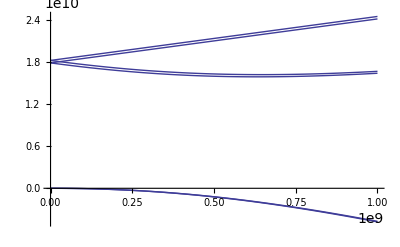

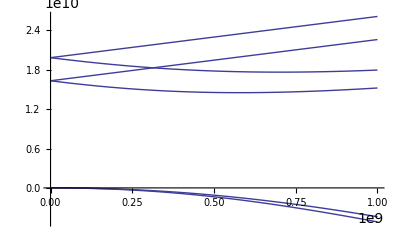

```mathematica
params={"B"->{B,0,0},"carbonPositions"->{{1,1}},"carbonHyperfineTensors"->{({{A, 0, 0}, {0, A, 0}, {0, 0, A}})}};
Simplify[NVHamiltonian[params],B>0]//MatrixForm
Plot[Eigenvalues[NVHamiltonian[params]/.B->10],{A,0,10^9}]
Plot[Eigenvalues[NVHamiltonian[params]/.B->100],{A,0,10^9}]
```

## NVHamiltonian: possible parameters

“Δ”					The ZFS tensor. Can be a number, a list of the diagonal elements, 
						or the full 3x3 tensor.
	“B”					The magnetic field in the lab frame in spherical coordinates ({B, θ, ϕ}, 
						where θ is the azimuthal angle, and ϕ is the polar angle). Units of
						Gauss.
	“crystalOrientation”			The Euler angles describing the orientation of the crystal lattice with 
						respect to the lab frame (ZYZ extrinsic convention).
	“nvOrientation”				An integer between 1 and 8 inclusive specifying the orientation of the 
						NV centre with respect to the lattice. See NVAngles
	“nitrogenIsotope”			The spin of the nitrogen (so either 14 or 15). Optionally, enter 0 to 
						ignore the nitrogen.
	“nitrogenHyperfineTensorSource”	If the nitrogen hyperfine tensor is being pulled from the literature, you 
						can specify the source here. See the “NV Parameters from Literature” 
						section for source names.
	“nitrogenQuadrapolarTensorSource”	If the nitrogen quadrapolar tensor is being pulled from the literature, 
						you can specify the source here. See the “NV Parameters from 
						Literature” section for source names.
	“carbonHyperfineTensorSource” 	If the carbon hyperfine tensors are being pulled from the literature, 
						you can specify the source here. See the “NV Parameters from Literature” 
						section for source names.
	“nitrogenHyperfineTensor”		The 3x3 nitrogen hyperfine tensor, or a list of the diagonal elements.
	“nitrogenQuadrapolarTensor”		The 3x3 nitrogen quadrapolar tensor, or a list of the diagonal elements.
	“carbonPositions “			A list of shell-index pairs, specifying which carbons have spin, 
						e.g. {{1,1},{1,2},{1,3}} for all three closest carbons. This is the order they 
						will take in the tensor product.
	“carbonHyperfineTensors”		A list of the 3x3 carbon hyperfine tensors (or diagonal elements), one for 
						each of the entries in carbonPositions.
	“zfsActivated”				True or False; whether the ZFS Hamiltonian is to be included.
	“nvZeemanActivated”			True or False; whether the NV Zeeman Hamiltonian is to be included.
	“nitrogenZeemanActivated”		True or False; whether the nitrogen Zeeman Hamiltonian is to be included.
	“carbonZeemanActivated”		True or False; whether the carbon Zeeman Hamiltonian is to be included.
	“nitogenQuadrapolarActivated”		True or False; whether the nitrogen quadrapolar Hamiltonian is to be included.
	“nitrogenHyperfineActivated”		True or False; whether the nitrogen hyperfine Hamiltonian is to be included.
	“carbonHyperfineActivated”		True or False; whether the carbon hyperfine Hamiltonian is to be included.
	“nitrogenCarbonDipolarActivated”	True or False; whether the nitrogen-carbon dipolar Hamiltonian is to be included.
	“carbonCarbonDipolarActivated”	True or False; whether the carbon-carbon dipolar Hamiltonian is to be included.
						
ALL of the above parameters are optional; it will pick default values for them if you don’t specify. 
Note: If you happen to both give a tensor and the source, it will choose to use the tensor you gave it instead of the tensor corresponding to the source.

## Visualizing the parameters

The function VisualizeNVParameters[params] can help you visualize where the B-field is pointing with respect to which carbons are active, etc. params is the same list that NVHamiltonian[params] accepts. Hover over the plot to see different tool tips.

```mathematica
params = {"carbonPositions"->{{1,1}},"B"->{10,0,π/2}}
NVHamiltonian[params]//MatrixForm
VisualizeNVParameters[params]
```

{carbonPositions→{{1,1}},B→{10,0,π/2}}

(1.89069×10^10 | -1.56774×10^8 | 1.36582×10^7 | 3.13569×10^8 | 0. | 0.
-1.56774×10^8 | 1.72843×10^10 | 1.38253×10^9 | 2.35385×10^8 | 0. | 0.
1.36582×10^7 | 1.38253×10^9 | 0. | 10705. | 1.36582×10^7 | 3.13569×10^8
3.13569×10^8 | 2.35385×10^8 | 10705. | 0. | 1.38253×10^9 | 2.35385×10^8
0. | 0. | 1.36582×10^7 | 1.38253×10^9 | 1.72843×10^10 | 1.56795×10^8
0. | 0. | 3.13569×10^8 | 2.35385×10^8 | 1.56795×10^8 | 1.89069×10^10)

-Graphics3D-